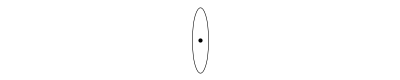

Y=0,  I_3=0

(ds-sd)(s̄d̄-d̄s̄)+(ud-du)(d̄ū-ūd̄)+(us-su)(s̄ū-ūs̄)

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T C(γ̄)^5 s_b-s_a^T C(γ̄)^5 d_b) ((d̄)_a(γ̄)^5 C((s̄)_b)^T)+(s_a^T C(γ̄)^5 d_b-d_a^T C(γ̄)^5 s_b) ((s̄)_a(γ̄)^5 C((d̄)_b)^T)+(s_a^T C(γ̄)^5 d_b) ((d̄)_b(γ̄)^5 C((s̄)_a)^T-(s̄)_b(γ̄)^5 C((d̄)_a)^T)+(d_a^T C(γ̄)^5 s_b) ((s̄)_b(γ̄)^5 C((d̄)_a)^T-(d̄)_b(γ̄)^5 C((s̄)_a)^T)+(s_a^T C1 d_b) ((d̄)_a 1C((s̄)_b)^T-(d̄)_b 1C((s̄)_a)^T)+(d_a^T C1 s_b-s_a^T C1 d_b) ((s̄)_a 1C((d̄)_b)^T)+(d_a^T C1 s_b) ((d̄)_b 1C((s̄)_a)^T-(s̄)_b 1C((d̄)_a)^T)-d_a^T C1 s_b(d̄)_a 1C((s̄)_b)^T+s_a^T C1 d_b(s̄)_b 1C((d̄)_a)^T+(d_a^T C(γ̄)^5 u_b-u_a^T C(γ̄)^5 d_b) ((d̄)_a(γ̄)^5 C((ū)_b)^T)+(u_a^T C(γ̄)^5 d_b-d_a^T C(γ̄)^5 u_b) ((ū)_a(γ̄)^5 C((d̄)_b)^T)+(u_a^T C(γ̄)^5 d_b) ((d̄)_b(γ̄)^5 C((ū)_a)^T-(ū)_b(γ̄)^5 C((d̄)_a)^T)+(d_a^T C(γ̄)^5 u_b) ((ū)_b(γ̄)^5 C((d̄)_a)^T-(d̄)_b(γ̄)^5 C((ū)_a)^T)+(u_a^T C1 d_b) ((d̄)_a 1C((ū)_b)^T-(d̄)_b 1C((ū)_a)^T)+(d_a^T C1 u_b-u_a^T C1 d_b) ((ū)_a 1C((d̄)_b)^T)+(d_a^T C1 u_b) ((d̄)_b 1C((ū)_a)^T-(ū)_b 1C((d̄)_a)^T)-d_a^T C1 u_b(d̄)_a 1C((ū)_b)^T+u_a^T C1 d_b(ū)_b 1C((d̄)_a)^T+(s_a^T C(γ̄)^5 u_b-u_a^T C(γ̄)^5 s_b) ((s̄)_a(γ̄)^5 C((ū)_b)^T)+(u_a^T C(γ̄)^5 s_b-s_a^T C(γ̄)^5 u_b) ((ū)_a(γ̄)^5 C((s̄)_b)^T)+(u_a^T C(γ̄)^5 s_b) ((s̄)_b(γ̄)^5 C((ū)_a)^T-(ū)_b(γ̄)^5 C((s̄)_a)^T)+(s_a^T C(γ̄)^5 u_b) ((ū)_b(γ̄)^5 C((s̄)_a)^T-(s̄)_b(γ̄)^5 C((ū)_a)^T)+(u_a^T C1 s_b) ((s̄)_a 1C((ū)_b)^T-(s̄)_b 1C((ū)_a)^T)+(s_a^T C1 u_b-u_a^T C1 s_b) ((ū)_a 1C((s̄)_b)^T)+(s_a^T C1 u_b) ((s̄)_b 1C((ū)_a)^T-(ū)_b 1C((s̄)_a)^T)-s_a^T C1 u_b(s̄)_a 1C((ū)_b)^T+u_a^T C1 s_b(ū)_b 1C((s̄)_a)^T

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-2 (d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 s)+2 (d̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 d)-2 (d̄ γ^μ d s̄ γ^μ s)+2 (d̄ γ^μ s s̄ γ^μ d)-2 (d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u)+2 (d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d)-2 (d̄ γ^μ d ū γ^μ u)+2 (d̄ γ^μ u ū γ^μ d)-2 (s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u)+2 (s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s)-2 (s̄ γ^μ s ū γ^μ u)+2 (s̄ γ^μ u ū γ^μ s)
```

Π(q^2)=
-(q^4 m_d log(-q^2/μ^2) ⟨ d̄ d⟩)/(3 π^4)+(64 m_d ⟨ d̄ d⟩ ⟨ s̄ s⟩^2)/(9 q^2)+(64 m_s ⟨ d̄ d⟩^2 ⟨ s̄ s⟩)/(9 q^2)+(64 m_d ⟨ d̄ d⟩ ⟨ ū u⟩^2)/(9 q^2)+(64 m_u ⟨ d̄ d⟩^2 ⟨ ū u⟩)/(9 q^2)-(q^4 m_s log(-q^2/μ^2) ⟨ s̄ s⟩)/(3 π^4)+(64 m_s ⟨ s̄ s⟩ ⟨ ū u⟩^2)/(9 q^2)+(64 m_u ⟨ s̄ s⟩^2 ⟨ ū u⟩)/(9 q^2)-(q^4 m_u log(-q^2/μ^2) ⟨ ū u⟩)/(3 π^4)-(q^2 log(-q^2/μ^2) ⟨G^3⟩)/(72 π^6)-(q^4 log(-q^2/μ^2) ⟨ GG ⟩)/(16 π^5)+(7 q^8 g_s^2 log^2(-q^2/μ^2))/(23040 π^8)-(11449 q^8 g_s^2 log(-q^2/μ^2))/(2419200 π^8)-(q^8 log(-q^2/μ^2))/(640 π^6)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

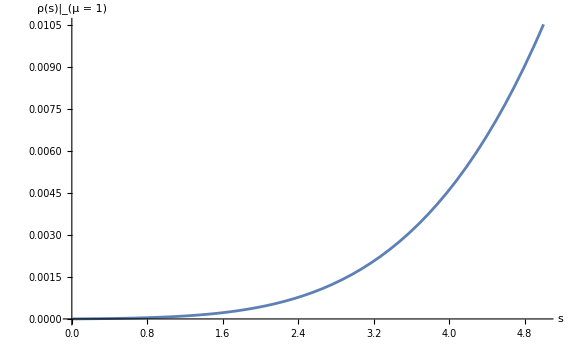
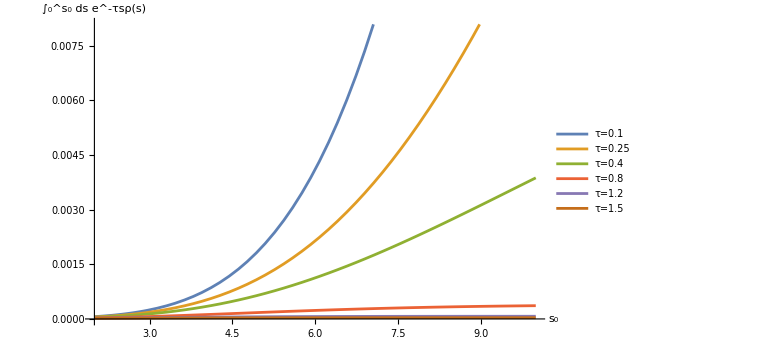

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

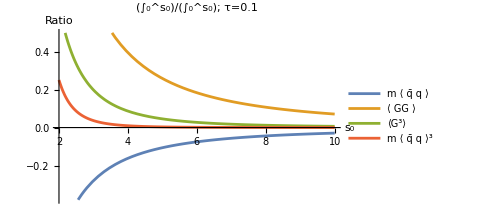
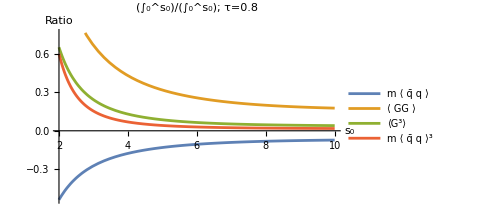
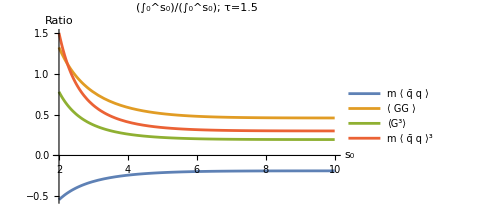

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

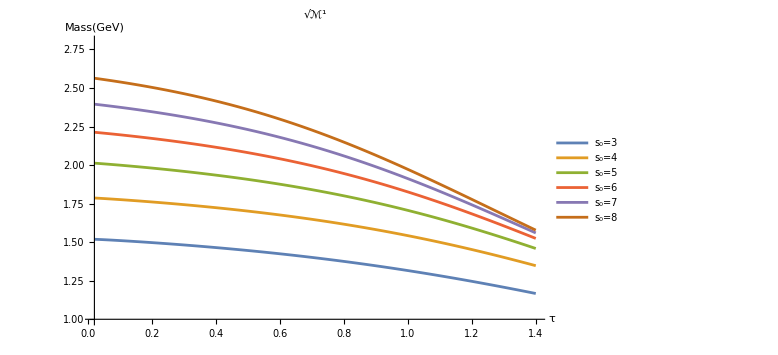
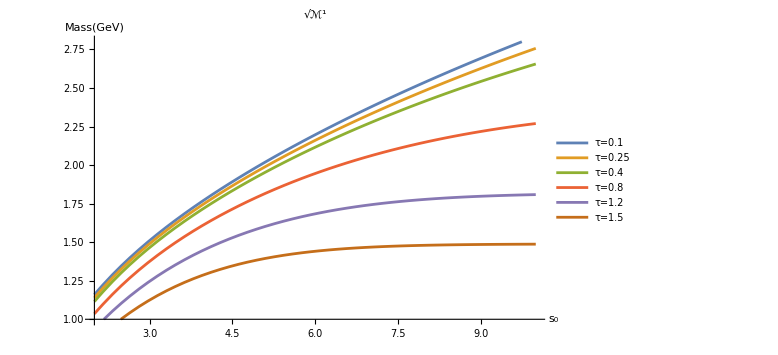

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

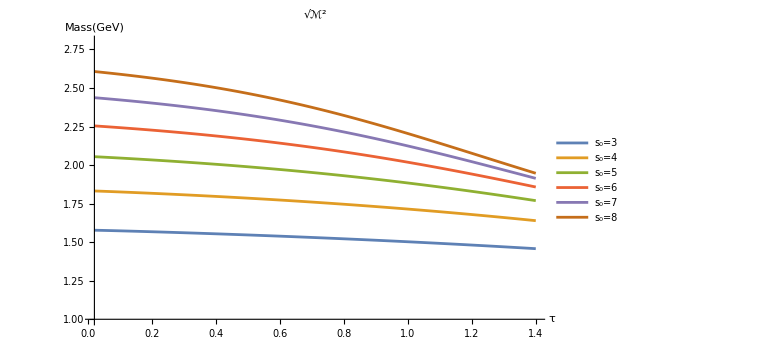
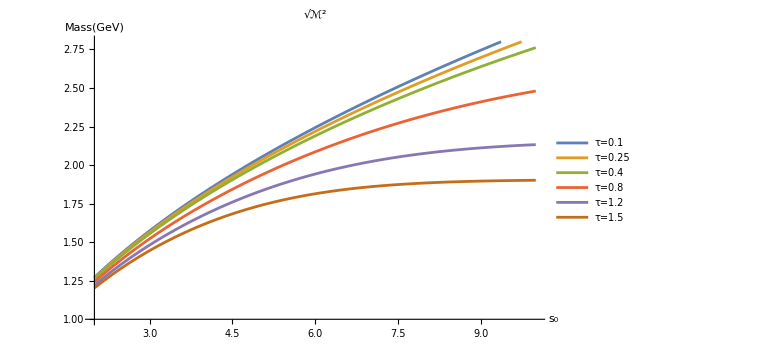

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

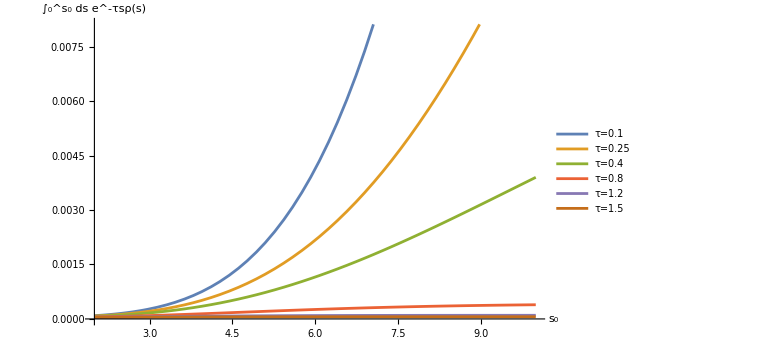
{-Graphics-,-Graphics-}

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

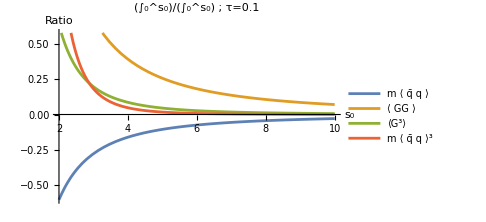
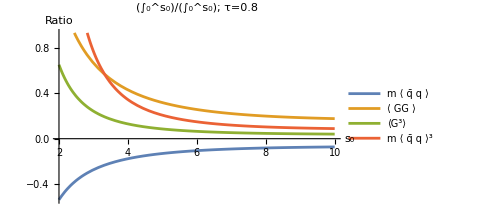
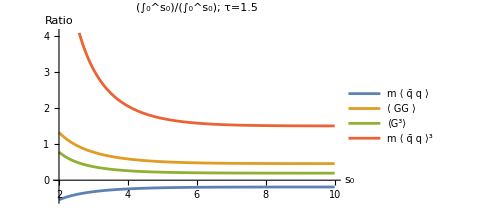

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

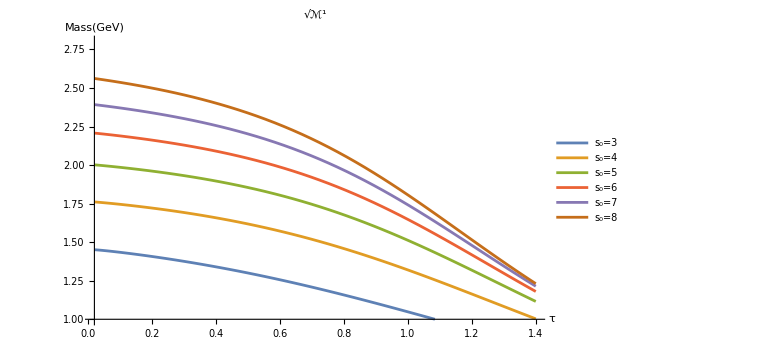
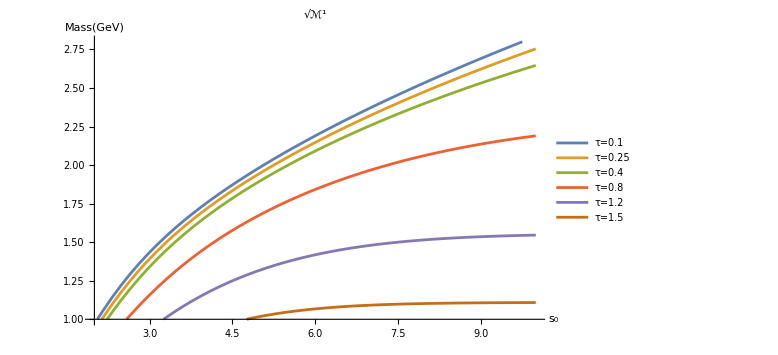

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5

{-Graphics-,-Graphics-}

```mathematica
(*-------------------------------*)
```